# Transmission coefficient as a function of energy

```mathematica
V[Ener_]=Piecewise[{{Subscript[V, 0], 1≤Ener≤a}, {0, True}}]/.Subscript[V, 0]->1;
```

```mathematica
T=1/(1+Subscript[V, 0]^2/(4 E (Subscript[V, 0]-Ener))Sinh[√((2 m(Subscript[V, 0]-Ener))/ℏ^2 a)]^2);
```

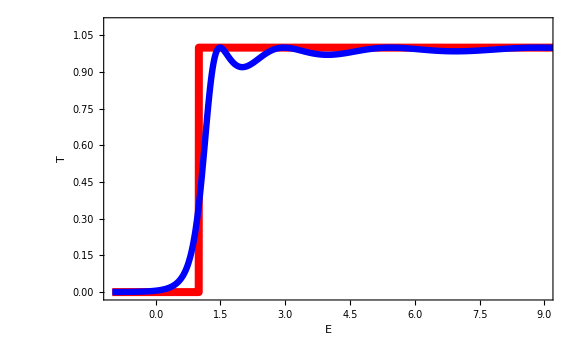

```mathematica
Plot[{V[Ener]/.{a->10},T/.{a->10,Subscript[V, 0]->1,ℏ->1,m->1}},{Ener,-1,10},
Frame->True,
FrameLabel->{"E","T"},FrameStyle->Black,PlotRange->{{-1.,9},{-0.01,1.1}},Exclusions->None,PlotStyle->{{Thickness@0.01,Red},{Thickness@0.008,Blue}},LabelStyle->Directive[Black,25],ImageSize->Large]
```

```mathematica
0
```